```mathematica
Clear["Global`*"]
```

```mathematica
F2[x_,y_]:=0.5*(x^4 - 16x^2 + 5x + y^4 - 16y^2 + 5y);
```

```mathematica
p =3; 
q = 7;
F1[x1_, x2_]:= (x1 - p)^2 + (x2 -q)^2-(2*x1*x2)/(p+q);

GradF1[x_,y_]= - ∇_{x,y} F1[x,y]
```

{-2 (-3+x)+y/5,x/5-2 (-7+y)}

```mathematica
N[{{x->730/99,y->370/99}}]
```

{{x→7.37374,y→3.73737}}

```mathematica
Plot3D[F1[x1,x2],{x1,-4+730/99,4+730/99},{x2,-4+370/99,4+370/99}]
```

-Graphics3D-

```mathematica
Δx1 = 0.01; 
Δx2 = 0.01;
Central[x1_,x2_]:= {(F1[x1 + Δx1,x2]-F1[x1-Δx1,x2])/(2 Δx1),(F1[x1 ,x2+Δx2]-F1[x1,x2-Δx2])/(2 Δx2)};
Central[-4,2]
```

{-14.4,-9.2}

```mathematica
Central2[x1_,x2_]:= {(F2[x1 + Δx1,x2]-F2[x1-Δx1,x2])/(2 Δx1),(F2[x1 ,x2+Δx2]-F2[x1,x2-Δx2])/(2 Δx2)};
GradF2[x_,y_]:= - Central2[x,y]
```

```mathematica
startx1 = 1;
startx2 = 4;
a =0.02;
X= Table[0,1000];
X[[1]]={startx1,startx2};

For[i = 1, i < 1000,i++,
X[[i+1]] = X[[i]]-a*Central2[X[[i]][[1]], X[[i]][[2]]];]
```

```mathematica
Print[X[[1000]]]
```

{2.74678,2.74678}

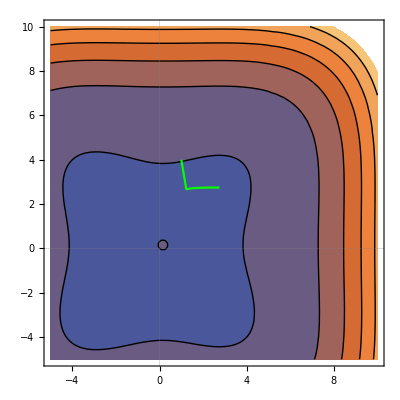

```mathematica
conpl2 = ContourPlot[F2[x1,x2],{x1,-5,10},{x2,-5,10},PlotTheme->"Scientific"];
vecpl2 =ListLinePlot[X,PlotRange->All,PlotStyle->Green];
Show[{conpl2,vecpl2}]
```